```mathematica
Quit
```

## Dlogbasis

```mathematica
SetDirectory[NotebookDirectory[]<>"../../"]
```

/Users/corradini/fire/FIRE6

```mathematica
<<DlogBasis`
```

DlogBasis: Package for automated calculation of leading singularities and dlog integrands.
Pascal Wasser, Johannes Gutenberg University Mainz (2020).

```mathematica
Internal= {k1, k2,k3};
External= {p1,p2,p3};
Propagators={-k1^2,-(k1+p1)^2,-(k1+p1+p2)^2,-(k2+p1+p2)^2,-k2^2,-(k2-k1)^2,-(k3-k2)^2,-(k3+p1+p2)^2,-(k3+p1+p2+p3)^2,-k3^2,-(k2+p1)^2,-(k2+p1+p2+p3)^2,-(k3+p1)^2,-(k1+p1+p2+p3)^2,-(k3+k1)^2};
Replacements= {p1^2->0,p2^2->0,p3^2->0,p1 p2->s/2,p1 p3->(-s-t)/2,p2 p3->t/2};
InitializeDlogbasis[];
```

```mathematica
SetParametrization[SpinorHelicityParametrization[Internal,{a,b,c},External]]
```

```mathematica
ansatz=IntegrandAnsatz[G[1,{1,1,1,1,1,1,1,1,1,1,0,0,0,0,0}]];
```

```mathematica
ansatz//Length
```

140

```mathematica
integrand=Parametrize[ansatz,n];
```

```mathematica
leadingsingularities=LeadingSingularities[integrand,IntegrandVariables[],n];
```

$Aborted

```mathematica
dlogs=GenerateDlogbasis[ansatz,leadingsingularities,n];
```

```mathematica
Export["FF/3LLad/dlog.m",(Cases[dlogs,_G,{0,Infinity}]/.{G[1,{a__}]:>{1,{a}}})//DeleteDuplicates]
Export["FF/3LLad/dlogBasis.m",dlogs]
```

FF/3LLad/dlog.m

FF/3LLad/dlogBasis.m

```mathematica
Quit[]
```

## Reduction using FIRE

```mathematica
SetDirectory[NotebookDirectory[]<>"../../"];
Get["FIRE6.m"];
```

FIRE, version 6.5.2

```mathematica
Internal= {k1, k2,k3};
External= {p1,p2,p3};
Propagators={-k1^2,-(k1+p1)^2,-(k1+p1+p2)^2,-(k2+p1+p2)^2,-k2^2,-(k2-k1)^2,-(k3-k2)^2,-(k3+p1+p2)^2,-(k3+p1+p2+p3)^2,-k3^2,-(k2+p1)^2,-(k2+p1+p2+p3)^2,-(k3+p1)^2,-(k1+p1+p2+p3)^2,-(k3+k1)^2};
Replacements= {p1^2->0,p2^2->0,p3^2->0,p1 p2->s/2,p1 p3->(-s-t)/2,p2 p3->t/2};
```

```mathematica
PrepareIBP[];
Prepare[AutoDetectRestrictions->True,LI->True];
SaveStart["FF/3LLad/3LLad"];
Quit[];
```

Prepared

Dimension set to 15

No symmetries

Saving initial data

```mathematica
SetDirectory[NotebookDirectory[]<>"../../"];
SetDirectory["extra/LiteRed/Setup/"];
Get["LiteRed.m"];
SetDirectory["../../.."];
Get["FIRE6.m"];
Internal= {k1, k2,k3};
External= {p1,p2,p3};
Propagators={-k1^2,-(k1+p1)^2,-(k1+p1+p2)^2,-(k2+p1+p2)^2,-k2^2,-(k2-k1)^2,-(k3-k2)^2,-(k3+p1+p2)^2,-(k3+p1+p2+p3)^2,-k3^2,-(k2+p1)^2,-(k2+p1+p2+p3)^2,-(k3+p1)^2,-(k1+p1+p2+p3)^2,-(k3+k1)^2};
Replacements= {p1^2->0,p2^2->0,p3^2->0,p1 p2->s/2,p1 p3->(-s-t)/2,p2 p3->t/2};
CreateNewBasis[b1,Directory->"./b3LLad.dir"];
GenerateIBP[b1];
AnalyzeSectors[b1,{__,0,0,0,0,0}];
FindSymmetries[b1,EMs->True];
DiskSave[b1];
Quit[];
```

**************** LiteRed v1.83 ********************
Author: Roman N. Lee, Budker Institute of Nuclear Physics, Novosibirsk.
Release Date: 11.01.2020
LiteRed stands for Loop InTEgrals REDuction.
The package is designed for the search and application of the Integration-By-Part reduction rules. It also contains some other useful tools.
Input file timestamp: Sun 7 Sep 2025 15:59:28
See ?LiteRed`* for a list of functions.

FIRE, version 6.5.2

Declare: {{k1,k2,k3,p1,p2,p3},Vector,{s,t},Number}

Lee propagators: {-(k1·k1),-((k1+p1)·(k1+p1)),-((k1+p1+p2)·(k1+p1+p2)),-((k2+p1+p2)·(k2+p1+p2)),-(k2·k2),-((-k1+k2)·(-k1+k2)),-((-k2+k3)·(-k2+k3)),-((k3+p1+p2)·(k3+p1+p2)),-((k3+p1+p2+p3)·(k3+p1+p2+p3)),-(k3·k3),-((k2+p1)·(k2+p1)),-((k2+p1+p2+p3)·(k2+p1+p2+p3)),-((k3+p1)·(k3+p1)),-((k1+p1+p2+p3)·(k1+p1+p2+p3)),-((k1+k3)·(k1+k3))}

Valid basis.\n    Ds[b1] — denominators,\n    SPs[b1] — scalar products involving loop momenta,\n    LMs[b1] — loop momenta,\n    EMs[b1] — external momenta,\n    Toj[b1] — rules to transform scalar products to denominators.\nThe definitions of the basis will be saved in ./b3LLad.dir

DiskSave::dir: The directory ./b3Llad.dir has been created.

Integration-By-Part&Lorentz-Invariance identities are generated.
    IBP[b1] — integration-by-part identities,
    LI[b1] — Lorentz invariance identities.

Found 784 zero sectors out of 1024.
    ZeroSectors[b1] — zero sectors,
    NonZeroSectors[b1] — nonzero sectors,
    SimpleSectors[b1] — simple sectors (no nonzero subsectors),
    BasisSectors[b1] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[b1] — a rule to nullify all zero j[b1…],
    CutDs[b1] — a flag list of cut denominatorsj (1=cut).

Found 163 mapped sectors and 77 unique sectors.
    UniqueSectors[b1] — unique sectors.
    MappedSectors[b1] — mapped sectors.
    SR[b1][…] — symmetry relations for j[b1,…] from UniqueSectors[b1].
    jSymmetries[b1,…] — symmetry rules for the sector js[b1,…] in UniqueSectors[b1].
    jRules[b1,…] — reduction rules for j[b1,…] from MappedSectors[b1].

DiskSave::overwrite: The file ./b3Llad.dir/b1 has been overwritten.

```mathematica
SetDirectory[NotebookDirectory[]<>"../../"];
Get["FIRE6.m"];
LoadStart["FF/3LLad/3LLad"];
TransformRules["./b3LLad.dir","FF/3LLad/3LLad.lbases",1];
SaveSBases["FF/3LLad/3LLad"];
Quit[];
```

```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../../"];
Get["FIRE6.m"];
LoadStart["FF/3LLad/3LLad",1];
Burn[];
LoadTables["FF/3LLad/3LLad.tables"];
```

FIRE, version 6.5.2

Initial data loaded

```mathematica
InvCh=(Import["FF/3LLad/dlogBasis.m"]/.{G->F});
```

```mathematica
InvCh//Length
```

101

```mathematica
Export["FF/3LLad/mastersLad.m",F[1,{1,1,1,1,1,1,1,1,1,1,0,0,0,0,0}]];
Export["FF/3LLad/mastersLadCan.m",MasterIntegrals[]];
Export["FF/3LLad/invCh.m",InvCh];
```

## Change of basis from the canonical basis to the ‘Laporta’ one

```mathematica
Quit
```

```mathematica
<<FiniteFlow`
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../../"];
```

```mathematica
Can=Import["FF/3LLad/dlogBasis.m"];
InvCh=Import["FF/3LLad/invCh.m"];
masters=Import["FF/3LLad/mastersLadCan.m"]/.{{1,{a__}}->G[1,{a}]};
```

```mathematica
cs=Table[c[i],{i,1,Length[InvCh]}];
```

```mathematica
eqs=Table[
Coefficient[cs[[i]]InvCh[[i]],
masters],{i,Length[InvCh]}];
```

```mathematica
mysys = Thread[Total[eqs]==0]//Collect[#,_c,Together]&;
```

```mathematica
mysol = FFDenseSolve[mysys,Reverse[cs]];
```

```mathematica
todel=((Cases[cs/.mysol,_c,Infinity]//DeleteDuplicates)/.c->List);
```

```mathematica
newCh=Delete[InvCh,todel];
newCan=Delete[Can,todel];
```

```mathematica
ChMat=Table[
Coefficient[newCh[[i]],
masters[[k]]],{i,Length[newCh]},{k,Length[masters]}];
```

```mathematica
Export["FF/3LLad/can.m",newCan];
Export["FF/3LLad/BasisCh.m",newCh];
```

```mathematica
Quit
```

```mathematica
masters=Import["FF/3LLad/mastersLadCan.m"]/.{_,{a__}}:>G[1,{a}];
MIstoCan=Import["FF/3LLad/MIstoCan.m"];
can=Import["FF/3LLad/can.m"];
MIstoCanRules=Thread[masters->MIstoCan.can];
BoxInCan=(Import["FF/3LLad/mastersLad.m"])/.MIstoCanRules;
```

```mathematica
Export["FF/3LLad/BoxinCan.m",BoxInCan];
```

## Append in one more needed UT integral

```mathematica
Quit
```

```mathematica
<<FiniteFlow`
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../../"];
```

```mathematica
can=Import["FF/3LLad/can.m"];
Chcom=(Import["FF/3LLad/BasisCh.m"]);
ChMat=Table[
Coefficient[Chcom[[i]],
masters[[k]]],{i,Length[Chcom]},{k,Length[masters]}];
masters=Import["FF/3LLad/mastersLadCan.m"]/.{_,{a__}}:>G[1,{a}];
```

```mathematica
FFInverse[Join[ChMat//Together,{IdentityMatrix[26][[1]]}]]
```

```mathematica
masters[[1]]
```

G[1,{0,0,1,0,0,1,1,0,0,1,0,0,0,0,0}]

```mathematica
NextWanted=s/( eps^3)G[1,{0,0,2,0,0,2,2,0,0,1,0,0,0,0,0}];
Export["FF/3LLad/cancom.m",Join[can,{NextWanted}]];
Export["FF/3LLad/UTAddenda.m",Cases[NextWanted,_G]/.{G[_,{a__}]:>{1,{a}}}];
```

### Compute IBPs for the additional integral using 3LLadUTAdd.config

```mathematica
SetDirectory[NotebookDirectory[]<>"../../"];
Get["FIRE6.m"];
LoadStart["FF/3LLad/3LLad",1];
Burn[];
LoadTables["FF/3LLad/3LLadUTAdd.tables"];
```

FIRE, version 6.5.2

Initial data loaded

```mathematica
FinalUT=Table[
Coefficient[NextWanted/.{G[_,{a__}]:>F[1,{a}]},
masters[[k]]],{k,Length[masters]}];
```

```mathematica
Export["FF/3LLad/BasisChcom.m",Join[Chcom,{NextWanted/.{G[_,{a__}]:>F[1,{a}]}}]]
```

FF/3LLad/BasisChcom.m

```mathematica
BasisChange=FFInverse[Join[ChMat/.{d->4-2eps}//Together,{FinalUT}/.{d->4-2eps}]];
Export["FF/3LLad/MIstoCan.m",BasisChange];
```

## Draw MIs

```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../../"];
```

```mathematica
<<LiteRed2`
```

**************** LiteRed v2.025β ********************
Author: Roman N. Lee, Budker Institute of Nuclear Physics, Novosibirsk.
Release Date: ????-??-??
Timestamp: Thu 20 Nov 2025 13:50:10
Read from:/Users/corradini/LiteRed2/Source/LiteRed2025.m (CRC32:749265139,{2340977437, 3317197336, 1063727846})

LiteRed stands for Loop integrals Reduction.
The package is designed for the search and application of the Integration-By-Part reduction rules. It also contains some other useful tools.

See ?LiteRed`* for a list of functions.

```mathematica
Declare[{k1,k2,k3,p1,p2,p3},Vector,{s,t},Number];
```

```mathematica
sp[p1,p1]=0;sp[p2,p2]=0;sp[p3,p3]=0;sp[p1,p2]=s/2;sp[p2,p3]=t/2;sp[p1,p3]=(-s-t)/2;
```

```mathematica
NewDsBasis[box3,{-(k1·k1),-((k1+p1)·(k1+p1)),-((k1+p1+p2)·(k1+p1+p2)),-((k2+p1+p2)·(k2+p1+p2)),-(k2·k2),-((-k1+k2)·(-k1+k2)),-((-k2+k3)·(-k2+k3)),-((k3+p1+p2)·(k3+p1+p2)),-((k3+p1+p2+p3)·(k3+p1+p2+p3)),-(k3·k3),-((k2+p1)·(k2+p1)),-((k2+p1+p2+p3)·(k2+p1+p2+p3)),-((k3+p1)·(k3+p1)),-((k1+p1+p2+p3)·(k1+p1+p2+p3)),-((k1+k3)·(k1+k3))},{k1,k2,k3},Directory->"box3dir"];
```

box3 is valid basis. The definitions of the basis will be saved in "box3dir" directory.
    Ds[box3] — denominators,
    SPs[box3] — scalar products involving loop momenta,
    LMs[box3] — loop momenta,
    EMs[box3] — external momenta,
    Parameters[box3] — parameters (invariants, masses, dimension),
    Toj[box3] — rules to transform scalar products to denominators,
    CutDs[box3] — flag vector of cut denominators.

```mathematica
topo={{8->1,0},{1->2,0},{2->3,0},{3->4,0},{7->8,0},{8->3,0},{4->7,0},{4->5,0},{5->6,0},{6->7,0},{-1->1,p1,0},{-2->2,p2,0},{-5->5,p3,0},{-6->6,p4,0}};
```

```mathematica
SetOptions[FeynGraphPlot,EdgeLabels->True,Frame->False]
```

{GraphLayout→SpringElectricalEmbedding,VertexCoordinates→Automatic,EdgeLabels→True,EdgeStyle→{_→{GrayLevel[0]}},VertexStyle→{_→{GrayLevel[0],Disk[{0,0}]}},VertexSize→{_→0.003},VertexLabels→None,VertexLabelStyle→{RGBColor[1, 0, 0]},Background→None,Frame→False,FrameLabel→None,FrameStyle→{},LabelStyle→{},ImageMargins→0,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→RGBColor[1, 0, 0],MultiedgeStyle→Automatic,PackingMethod→Automatic,PlotLabel→None,Epilog→{}}

```mathematica
AttachGraph[js[box3,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0],topo]
```

```mathematica
masters=Import["FF/3LLad/mastersLadCan.m"]/.{_,{a__}}:>j[box3,a]
```

{j[box3,0,0,1,0,0,1,1,0,0,1,0,0,0,0,0],j[box3,0,0,1,0,1,1,0,1,0,1,0,0,0,0,0],j[box3,0,0,1,0,1,1,1,0,1,0,0,0,0,0,0],j[box3,0,0,1,0,1,1,1,1,0,0,0,0,0,0,0],j[box3,0,1,0,0,0,1,1,0,1,0,0,0,0,0,0],j[box3,0,1,0,0,0,1,1,1,0,1,0,0,0,0,0],j[box3,0,1,0,0,0,1,1,1,1,1,0,0,0,0,0],j[box3,0,1,0,0,1,1,1,1,1,0,0,0,0,0,0],j[box3,0,1,0,1,1,1,0,1,0,1,0,0,0,0,0],j[box3,0,1,0,1,1,1,1,0,1,0,0,0,0,0,0],j[box3,0,1,0,1,1,1,1,0,2,0,0,0,0,0,0],j[box3,0,1,0,1,1,1,1,1,1,1,0,0,0,0,0],j[box3,0,1,0,1,1,1,1,1,2,1,0,0,0,0,0],j[box3,0,1,1,0,0,1,1,0,1,1,0,0,0,0,0],j[box3,0,1,1,0,1,1,1,1,0,1,0,0,0,0,0],j[box3,0,1,1,0,1,1,1,1,1,0,0,0,0,0,0],j[box3,0,1,1,0,1,1,1,1,1,1,0,0,0,0,0],j[box3,0,1,1,0,1,1,1,1,1,2,0,0,0,0,0],j[box3,0,1,1,0,1,1,1,1,2,0,0,0,0,0,0],j[box3,1,0,1,0,0,1,1,1,0,1,0,0,0,0,0],j[box3,1,0,1,1,1,0,0,1,0,1,0,0,0,0,0],j[box3,1,1,1,0,0,1,1,1,1,1,0,0,0,0,0],j[box3,1,1,1,0,0,1,1,1,2,1,0,0,0,0,0],j[box3,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0],j[box3,1,1,1,1,1,1,1,1,1,1,-1,0,0,0,0],j[box3,1,1,1,1,1,1,1,1,2,1,0,0,0,0,0]}

jGraph::nums: The numerator is not drawn!.

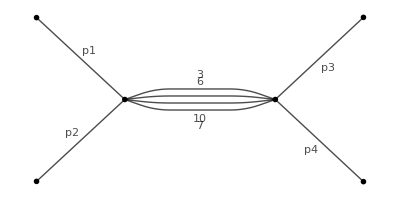
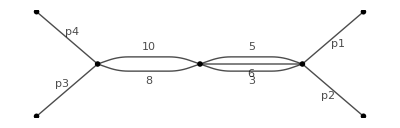
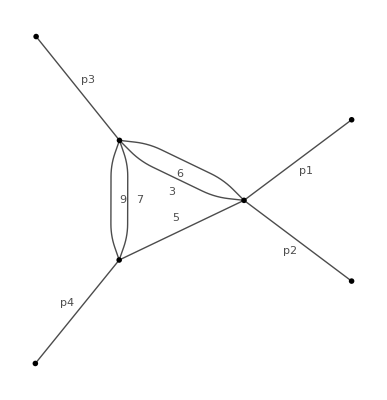
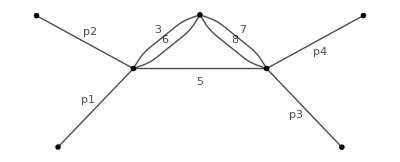
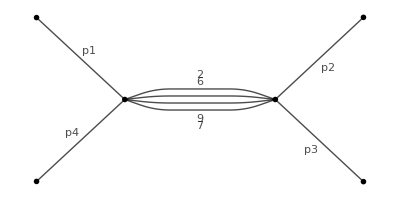
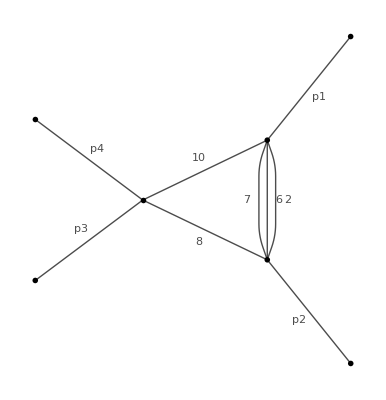
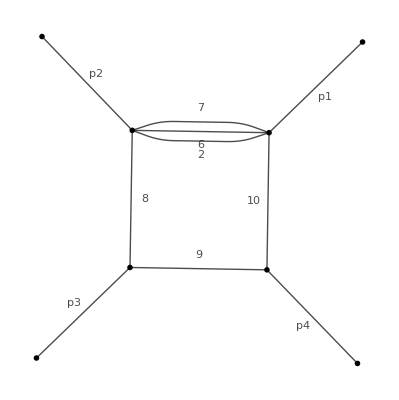
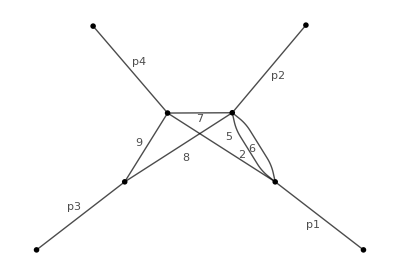
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
jGraphPlot/@masters
```

```mathematica
canonicalmasters=Import["FF/3LLad/cancom.m"]/.{_,{a__}}:>j[box3,a];
canonicalmastersinMI=Import["FF/3LLad/BasisChcom.m"]/.{_,{a__}}:>j[box3,a];
```

```mathematica
SetOptions[FeynGraphPlot,EdgeLabels->False,Frame->False]
```

{GraphLayout→SpringElectricalEmbedding,VertexCoordinates→Automatic,EdgeLabels→False,EdgeStyle→{_→{GrayLevel[0]}},VertexStyle→{_→{GrayLevel[0],Disk[{0,0}]}},VertexSize→{_→0.003},VertexLabels→None,VertexLabelStyle→{RGBColor[1, 0, 0]},Background→None,Frame→False,FrameLabel→None,FrameStyle→{},LabelStyle→{},ImageMargins→0,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→RGBColor[1, 0, 0],MultiedgeStyle→Automatic,PackingMethod→Automatic,PlotLabel→None,Epilog→{}}

jGraph::nums: The numerator is not drawn!.

General::stop: Further output of jGraph::nums will be suppressed during this calculation.

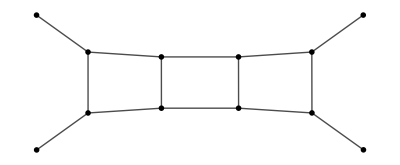
s^3 -Graphics-

```mathematica
(canonicalmasters/.Thread[Cases[canonicalmasters,_G,Infinity]->jGraphPlot/@(Cases[canonicalmasters,_G,Infinity]/.G[_,{a__}]:>j[box3,a])])[[20]]
```

```mathematica
Quit
```

```mathematica
masters=Import["FF/3LLad/mastersLadCan.m"]/.{_,{a__}}:>G[1,{a}];
```

## Differential equations matrix

```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../../"];
```

```mathematica
<<LiteRed2`
```

**************** LiteRed v2.025β ********************
Author: Roman N. Lee, Budker Institute of Nuclear Physics, Novosibirsk.
Release Date: ????-??-??
Timestamp: Thu 20 Nov 2025 13:50:10
Read from:/Users/corradini/LiteRed2/Source/LiteRed2025.m (CRC32:749265139,{2340977437, 3317197336, 1063727846})

LiteRed stands for Loop integrals Reduction.
The package is designed for the search and application of the Integration-By-Part reduction rules. It also contains some other useful tools.

See ?LiteRed`* for a list of functions.

```mathematica
Declare[{k1,k2,k3,p1,p2,p3},Vector,{s,t},Number];
sp[p1,p1]=0;sp[p2,p2]=0;sp[p3,p3]=0;sp[p1,p2]=s/2;sp[p2,p3]=t/2;sp[p1,p3]=(-s-t)/2;
```

```mathematica
NewDsBasis[box3,{-(k1·k1),-((k1+p1)·(k1+p1)),-((k1+p1+p2)·(k1+p1+p2)),-((k2+p1+p2)·(k2+p1+p2)),-(k2·k2),-((-k1+k2)·(-k1+k2)),-((-k2+k3)·(-k2+k3)),-((k3+p1+p2)·(k3+p1+p2)),-((k3+p1+p2+p3)·(k3+p1+p2+p3)),-(k3·k3),-((k2+p1)·(k2+p1)),-((k2+p1+p2+p3)·(k2+p1+p2+p3)),-((k3+p1)·(k3+p1)),-((k1+p1+p2+p3)·(k1+p1+p2+p3)),-((k1+k3)·(k1+k3))},{k1,k2,k3},Directory->"box3dir"];
```

box3 is valid basis. The definitions of the basis will be saved in "box3dir" directory.
    Ds[box3] — denominators,
    SPs[box3] — scalar products involving loop momenta,
    LMs[box3] — loop momenta,
    EMs[box3] — external momenta,
    Parameters[box3] — parameters (invariants, masses, dimension),
    Toj[box3] — rules to transform scalar products to denominators,
    CutDs[box3] — flag vector of cut denominators.

```mathematica
GenerateIBP[box3]
AnalyzeSectors[box3,{__,0,0,0,0,0}]
FindSymmetries[box3]
```

Identities are generated.
    IBP[box3] — integration-by-part identities,
    LI[box3] — Lorentz invariance identities.

Updated SectorsPattern[box3] — pattern for all relevant sectors of the basis box3.

Found 784(240) zero(nonzero) sectors out of 1024.
    ZeroSectors[box3] — zero sectors,
    NonZeroSectors[box3] — nonzero sectors,
    SimpleSectors[box3] — simple sectors (no nonzero subsectors),
    BasisSectors[box3] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[box3] — a rule to nullify all zero j[box3…],
    CutDs[box3] — a flag list of cut denominators (1=cut).

Found 163 mapped sectors and 77 unique sectors.
    UniqueSectors[box3] — unique sectors.
    MappedSectors[box3] — mapped sectors.
    SR[box3][…] — symmetry relations for j[box3,…] from UniqueSectors[box3].
    jSymmetries[box3,…] — symmetry rules for the sector js[box3,…] in UniqueSectors[box3].
    jRules[box3,…] — reduction rules for j[box3,…] from MappedSectors[box3].
    SectorsMappings[box3] gives the list of mappings of all sectors from MappedSectors[box3] to UniqueSectors[box3].

163

```mathematica
SectorOf[family_,exponents___]:=js[family,##]&@@(If[#>0,1,0]&/@{exponents});
SectorOf[j[family_,exponents___]]:=SectorOf[family,exponents];
```

```mathematica
ZeroQ[j[family_,a__]]:=MemberQ[ZeroSectors[family],SectorOf[j[family,a]]];
```

```mathematica
RemoveZeroSectors[expr_]:=expr /. Dispatch[(#->0)&/@Select[Cases[{expr},_j,Infinity]//DeleteDuplicates,ZeroQ]];
```

```mathematica
can=Import["FF/3LLad/BasisChcom.m"]/.G[_,{a__}]:>j[box3,a];
```

```mathematica
ders=Dinv[#,s]&/@can//RemoveZeroSectors;
dert=Dinv[#,t]&/@can//RemoveZeroSectors;
```

```mathematica
Export["FF/3LLad/ders.m",ders];
Export["FF/3LLad/dert.m",dert];
```

```mathematica
jsder=Cases[Join[ders,dert],_j,Infinity]//DeleteDuplicates;
```

```mathematica
Export["FF/3LLad/wishlist_der.m",jsder/.{j[box3,a__]:>{1,{a}}}];
```

```mathematica
Quit
```

### Run IBP reduction with 3LLadDer.config

## Build DE matrix

```mathematica
Quit
```

```mathematica
mastersLaporta=Import["FF/3LLad/mastersLadCan.m"];
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../../"];
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../../"];
Get["FIRE6.m"];
LoadStart["FF/3LLad/3LLad",1];
Burn[];
LoadTables["FF/3LLad/3LLadDer.tables"];
```

FIRE, version 6.5.2

Initial data loaded

```mathematica
masters=MasterIntegrals[];
```

```mathematica
SameQ[mastersLaporta,masters]
```

True

```mathematica
ders=(Import["FF/3LLad/ders.m"]/.j[_,a__]:>F[1,{a}]);
dert=(Import["FF/3LLad/dert.m"]/.j[_,a__]:>F[1,{a}]);
ders//Length
```

26

```mathematica
ds0=Table[Coefficient[ders[[i]],(masters[[k]]/.{{1,{a__}}:>G[1,{a}]})],{i,Length[ders]},{k,Length[masters]}];
dt0=Table[Coefficient[dert[[i]],(masters[[k]]/.{{1,{a__}}:>G[1,{a}]})],{i,Length[ders]},{k,Length[masters]}];
```

```mathematica
MIstoCanMatrix=(Import["FF/3LLad/MIstoCan.m"])/.{ϵ->eps};
```

```mathematica
ds=((ds0.MIstoCanMatrix)/.{d->4-2 eps})//Simplify;
dt=((dt0.MIstoCanMatrix)/.{d->4-2 eps})//Simplify;
```

```mathematica
Export["FF/3LLad/ds.m",ds];
Export["FF/3LLad/dt.m",dt];
```

```mathematica
ds=Import["FF/3LLad/ds.m"];
dt=Import["FF/3LLad/dt.m"];
```

## A first check: scaling and integrability conditions

```mathematica
s ds+t dt//Simplify//MatrixForm
```

(-3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 eps)

```mathematica
ds.dt-dt.ds-D[ds,t]+D[dt,s]//Simplify//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

## Integrating the equations

## Computing matrix logarithmic form in x=t/s

```mathematica
alphaco={s,t,s+t}
```

{s,t,s+t}

```mathematica
cs=c/@Range[Length[alphaco]];
```

```mathematica
eqss=Table[Table[eqs[ii,jj],{jj,1,Length[ds]}],{ii,1,Length[ds]}];
eqts=Table[Table[eqt[ii,jj],{jj,1,Length[dt]}],{ii,1,Length[dt]}];
```

```mathematica
Do[eqs[ii,jj]=ds[[ii]][[jj]]==D[cs.(Log[#]&/@alphaco),s],{ii,1,Length[ds]},{jj,1,Length[ds]}];
Do[eqt[ii,jj]=dt[[ii]][[jj]]==D[cs.(Log[#]&/@alphaco),t],{ii,1,Length[dt]},{jj,1,Length[dt]}];
```

```mathematica
num50=Table[{s->RandomReal[WorkingPrecision->50],t->RandomReal[WorkingPrecision->50]},{i,1,50}];
```

```mathematica
Do[Do[Asol[ii,jj]=NSolve[Flatten[Table[{eqs[ii,jj],eqt[ii,jj]}/.num50[[iter]],{iter,1,20}]],cs]//Chop//Rationalize;If[Mod[ii,50]==0&&Mod[jj,50]==0,PrintTemporary["Done :: {",ii,",",jj,"}"]];,{ii,1,Length[ds]}],{jj,1,Length[ds]}]
```

```mathematica
Atilde=Table[Table[(cs.(Log[#]&/@alphaco))/.Flatten[Asol[ii,jj]],{jj,1,Length[ds]}],{ii,1,Length[ds]}]/._c->0;
Atildex=Collect[Atilde/.t->x s/.s->-1/.Log[a___]:>PowerExpand[Log[Factor[a]]]/.Log[-1-x]:>Log[1+x]/.Pi->0,Log[___],Together];
```

```mathematica
Export["FF/3LLad/Atilde.m",Atildex]
```

FF/3LLad/Atilde.m

## Integrating the differential equations

```mathematica
Quit[]
```

```mathematica
<<PolyLogTools`;
```

(****** PolyLogTools 1.4 ******)

Authors: Claude Duhr, Falko Dulat

Email: cduhr@uni-bonn.de

PolyLogTools uses the implementation of the PSLQ algorithm by P. Bertok (http://library.wolfram.com/infocenter/MathSource/4263/)

*-*-*-*-*-* HPL 2.0 *-*-*-*-*-*

Author: Daniel Maitre, University of Zurich

Rules for minimal set loaded for weights: 2, 3, 4, 5, 6.

Rules for minimal set for + - weights loaded for weights: 2, 3, 4, 5, 6.

Table of MZVs loaded up to weight 6

Table of values at I loaded up to weight 6

$HPLFunctions gives a list of the functions of the package.
$HPLOptions gives a list of the options of the package.

More info in hep-ph/0507152, hep-ph/0703052 and at 
 http://krone.physik.unizh.ch/~maitreda/HPL/

GraphJoin::shdw: Symbol GraphJoin appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

GraphProduct::shdw: Symbol GraphProduct appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

GraphSum::shdw: Symbol GraphSum appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

SetDelayed::write: Tag EdgeChromaticNumber in EdgeChromaticNumber[g_Graph] is Protected.

SetDelayed::write: Tag TreeQ in TreeQ[g_Graph] is Protected.

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/corradini/fire/FIRE6/FF/3LLad

```mathematica
Atildex=Import["Atilde.m"];
```

```mathematica
Atildex//Variables
```

{eps,Log[x],Log[1+x]}

```mathematica
alphaco=Log[#]&/@{x,1+x};
```

### Weight 0

```mathematica
bdry0[0]=Table[b[i,0],{i,1,26}];
```

```mathematica
Table[A[i]=Coefficient[ Atildex,alphaco[[i]]],{i,1,2}];
```

```mathematica
Table[matexp[i]=MatrixExp[ Log[a] A[i]],{i,2}];
```

```mathematica
matexp[1]//Eigenvalues//DeleteDuplicates
```

{a^(-3 eps),1,a^eps,a^(3 eps)}

```mathematica
matexp[2]//Eigenvalues//DeleteDuplicates
```

{1,a^eps,a^(2 eps),a^(3 eps)}

```mathematica
eqs[1][0]=Thread[(Coefficient[matexp[1],a^(3eps)].(bdry0[0]))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[2][0]=Thread[(Coefficient[matexp[1],a^eps].(bdry0[0]))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[3][0]=Thread[(Coefficient[matexp[2],a^(3eps)].(bdry0[0]))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[4][0]=Thread[(Coefficient[matexp[2],a^(2eps)].(bdry0[0]))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[5][0]=Thread[(Coefficient[matexp[2],a^eps].(bdry0[0]))==0]//DeleteCases[#,True]&;
```

```mathematica
sols[1][0]=Solve[Join[Join[eqs[1][0],eqs[2][0],eqs[3][0],eqs[4][0],eqs[5][0]]],bdry0[0]][[1]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
bdryt[0]=bdry0[0]/.sols[1][0]
```

{-2 b[9,0]-1/2 b[25,0],-1/4 b[6,0]-1/3 b[9,0]+1/2 b[10,0]+2/3 b[15,0]-5/24 b[25,0],b[9,0]+1/4 b[25,0],0,b[9,0]+3/4 b[13,0]-1/2 b[15,0]+1/4 b[25,0],b[6,0],b[7,0],b[8,0],b[9,0],b[10,0],-1/2 b[6,0]+1/2 b[7,0]+1/2 b[8,0]+b[9,0]+b[13,0]+1/4 b[19,0],b[10,0],b[13,0],1/3 b[9,0]-2/3 b[15,0]+1/3 b[25,0],b[15,0],0,16/3 b[9,0]+4 b[13,0]-8/3 b[15,0]+4/3 b[25,0],0,b[19,0],-b[6,0]-1/2 b[19,0],-b[8,0]-2 b[9,0]-b[19,0],-b[6,0]-2 b[7,0]-3 b[13,0]-2 b[15,0]+1/2 b[25,0],0,8/3 b[9,0]+2 b[13,0]-4/3 b[15,0]+7/6 b[25,0],b[25,0],b[26,0]}

#### Weight 1

```mathematica
bdry0[1]=eps Table[b[i,1],{i,1,Length[bdry0[0]]}];
```

```mathematica
Mbt[1][0]=Map[GIntegrate[#,x]&,D[Simplify[Atildex.bdryt[0]],x]];
```

```mathematica
M0[1]=Mbt[1][0]+bdry0[1];
```

#### Fix remaining weight 0 constants

```mathematica
eqs[6][0]=Thread[(Im[Coefficient[matexp[2],a^eps].M0[1]/.x->-1]//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
eqs[7][0]=Thread[(Im[Coefficient[matexp[2],a^(2eps)].M0[1]/.x->-1]//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
```

```mathematica
sols[2][0]=Solve[Join[eqs[6][0],eqs[7][0]]/.{b[7,0]->b70},bdry0[0]][[1]]/.{Arg[a]->0}/.{b70->b[7,0]}
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{b[6,0]→16/9 b[7,0],b[8,0]→1/9 b[7,0],b[9,0]→7/9 b[7,0],b[10,0]→b[7,0],b[13,0]→0,b[15,0]→-2/3 b[7,0],b[19,0]→-64/9 b[7,0],b[25,0]→-28/9 b[7,0],b[26,0]→-4 b[7,0]}

```mathematica
bdryf[0]=bdryt[0]/.sols[2][0]/.{b[7,0]->-1/4};
```

```mathematica
Mf[0]=bdryf[0]
```

{0,0,0,0,-1/12,-4/9,-1/4,-1/36,-7/36,-1/4,1/3,-1/4,0,1/12,1/6,0,-4/9,0,16/9,-4/9,-49/36,1,0,1/6,7/9,1}

#### Fix weight 1 constants

```mathematica
Mbf[1][0]=Map[GIntegrate[#,x]&,D[Simplify[Atildex.bdryf[0]],x]];
```

```mathematica
Mt[1]=Mbf[1][0]+bdry0[1]
```

{eps b[1,1],eps b[2,1],eps b[3,1],eps b[4,1],eps b[5,1]+1/4 eps G[0,x],eps b[6,1]+4/3 eps G[0,x],eps b[7,1],eps b[8,1],eps b[9,1]+7/12 eps G[0,x],eps b[10,1]+3/4 eps G[0,x],eps b[11,1]-eps G[0,x],eps b[12,1]+3/4 eps G[0,x],eps b[13,1],eps b[14,1]-1/4 eps G[0,x],eps b[15,1]-1/2 eps G[0,x],eps b[16,1],eps b[17,1]+4/3 eps G[0,x],eps b[18,1],eps b[19,1]-11/3 eps G[0,x],eps b[20,1]+1/2 eps G[0,x],eps b[21,1]+5/2 eps G[0,x],eps b[22,1]-3/2 eps G[0,x],eps b[23,1],eps b[24,1]-1/2 eps G[0,x],eps b[25,1]-7/3 eps G[0,x],eps b[26,1]}

```mathematica
eqs[1][1]=Thread[(Coefficient[matexp[1],a^(3eps)].(Mt[1]/.x->0))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[2][1]=Thread[(Coefficient[matexp[1],a^eps].(Mt[1]/.x->0))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[3][1]=Thread[(Coefficient[matexp[2],a^(3eps)].(Mt[1]/.x->-1))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[4][1]=Thread[(Coefficient[matexp[2],a^(2eps)].(Mt[1]/.x->-1))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[5][1]=Thread[(Coefficient[matexp[2],a^eps].(Mt[1]/.x->-1))==0]//DeleteCases[#,True]&;
```

```mathematica
sols[1][1]=Solve[Join[Join[eqs[1][1],eqs[2][1],eqs[3][1],eqs[4][1],eqs[5][1]]],bdry0[1]/eps][[1]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
bdryt[1]=bdry0[1]/.sols[1][1]
```

{eps (-2 b[9,1]-1/2 b[25,1]),eps (-1/4 b[6,1]-1/3 b[9,1]+1/2 b[10,1]+2/3 b[15,1]-5/24 b[25,1]),eps (b[9,1]+1/4 b[25,1]),0,eps (b[9,1]+3/4 b[13,1]-1/2 b[15,1]+1/4 b[25,1]),eps b[6,1],eps b[7,1],eps b[8,1],eps b[9,1],eps b[10,1],eps (-1/2 b[6,1]+1/2 b[7,1]+1/2 b[8,1]+b[9,1]+b[13,1]+1/4 b[19,1]),eps b[10,1],eps b[13,1],eps (1/3 b[9,1]-2/3 b[15,1]+1/3 b[25,1]),eps b[15,1],0,eps (16/3 b[9,1]+4 b[13,1]-8/3 b[15,1]+4/3 b[25,1]),0,eps b[19,1],eps (-b[6,1]-1/2 b[19,1]),eps (-b[8,1]-2 b[9,1]-b[19,1]),eps (-b[6,1]-2 b[7,1]-3 b[13,1]-2 b[15,1]+1/2 b[25,1]),0,eps (8/3 b[9,1]+2 b[13,1]-4/3 b[15,1]+7/6 b[25,1]),eps b[25,1],eps b[26,1]}

### Weight 2

```mathematica
bdry0[2]=eps^2 Table[b[i,2],{i,1,Length[bdry0[0]]}];
Mbf[2][0]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[1][0])];
Mbt[1][1]=Map[GIntegrate[#,x]&,D[Atildex,x].bdryt[1]];
```

```mathematica
M0[2]=Mbf[2][0]+Mbt[1][1]+bdry0[2];
```

#### Fix remaining weight 1 constants

```mathematica
eqs[6][1]=Thread[(Im[Coefficient[matexp[2],a^eps].M0[2]/.x->-1]//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
eqs[7][1]=Thread[(Im[Coefficient[matexp[2],a^(2eps)].M0[2]/.x->-1]//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
```

```mathematica
sols[2][1]=Solve[Join[eqs[6][1],eqs[7][1]]/.{b[7,1]->b71},bdry0[1]/eps][[1]]/.{Arg[a]->0}/.{b71->b[7,1]}
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{b[6,1]→16/9 b[7,1],b[8,1]→1/9 b[7,1],b[9,1]→7/9 b[7,1],b[10,1]→b[7,1],b[13,1]→0,b[15,1]→-2/3 b[7,1],b[19,1]→-64/9 b[7,1],b[25,1]→-28/9 b[7,1],b[26,1]→-4 b[7,1]}

```mathematica
bdryf[1]=bdryt[1]/.sols[2][1]/.{b[7,1]->0};
```

```mathematica
Mf[1]=Mbf[1][0]+bdryf[1]
```

{0,0,0,0,1/4 eps G[0,x],4/3 eps G[0,x],0,0,7/12 eps G[0,x],3/4 eps G[0,x],-eps G[0,x],3/4 eps G[0,x],0,-1/4 eps G[0,x],-1/2 eps G[0,x],0,4/3 eps G[0,x],0,-11/3 eps G[0,x],1/2 eps G[0,x],5/2 eps G[0,x],-3/2 eps G[0,x],0,-1/2 eps G[0,x],-7/3 eps G[0,x],0}

#### Fix weight 2 constants

```mathematica
Mbf[1][1]=Map[GIntegrate[#,x]&,D[Atildex,x].bdryf[1]];
```

```mathematica
Mt[2]=Mbf[2][0]+Mbf[1][1]+bdry0[2];
```

```mathematica
eqs[1][2]=Thread[(Coefficient[matexp[1],a^(3eps)].(Mt[2]/.x->0))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[2][2]=Thread[(Coefficient[matexp[1],a^eps].(Mt[2]/.x->0))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[3][2]=Thread[(Coefficient[matexp[2],a^(3eps)].(Mt[2]/.x->-1))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[4][2]=Thread[(Coefficient[matexp[2],a^(2eps)].(Mt[2]/.x->-1))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[5][2]=Thread[(Coefficient[matexp[2],a^eps].(Mt[2]/.x->-1))==0]//DeleteCases[#,True]&;
```

```mathematica
sols[1][2]=Solve[Join[Join[eqs[1][2],eqs[2][2],eqs[3][2],eqs[4][2],eqs[5][2]]],bdry0[2]/eps^2][[1]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
bdryt[2]=bdry0[2]/.sols[1][2];
```

### Weight 3

```mathematica
bdry0[3]=eps^3 Table[b[i,3],{i,1,Length[bdry0[0]]}];
Mbf[3][0]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[2][0])];
Mbf[2][1]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[1][1])];
Mbt[1][2]=Map[GIntegrate[#,x]&,D[Atildex,x].bdryt[2]];
```

```mathematica
M0[3]=Mbf[3][0]+Mbf[2][1]+Mbt[1][2]+bdry0[3];
```

#### Fix remaining weight 2 constants

```mathematica
eqs[6][2]=Thread[(Im[Coefficient[matexp[2],a^eps].M0[3]/.x->-1]//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
eqs[7][2]=Thread[(Im[Coefficient[matexp[2],a^(2eps)].M0[3]/.x->-1]//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
```

```mathematica
sols[2][2]=Solve[Join[eqs[6][2],eqs[7][2]]/.{b[7,2]->b72},bdry0[2]/eps^2][[1]]/.{Arg[a]->0}/.{b72->b[7,2]}
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{b[6,2]→(2 (π^3+8 π b[7,2]))/(9 π),b[8,2]→-(π^3-2 π b[7,2])/(18 π),b[9,2]→-(π^3-28 π b[7,2])/(36 π),b[10,2]→-(-13 π^3-12 π b[7,2])/(12 π),b[13,2]→π^2/9,b[15,2]→-2/3 b[7,2],b[19,2]→-(51 π^3+128 π b[7,2])/(18 π),b[25,2]→-(-π^3+28 π b[7,2])/(9 π),b[26,2]→-(π^3+4 π b[7,2])/π}

```mathematica
bdryf[2]=bdryt[2]/.sols[2][2]/.{b[7,2]->-π^2/4};
```

```mathematica
Mf[2]=Mbf[2][0]+Mbf[1][1]+bdryf[2]
```

{0,-1/36 eps^2 π^2,0,0,-3/4 eps^2 G[0,0,x],-2/9 eps^2 π^2-4 eps^2 G[0,0,x],-1/4 eps^2 π^2,-1/12 eps^2 π^2,-2/9 eps^2 π^2-7/4 eps^2 G[0,0,x],(5 eps^2 π^2)/6-1/4 eps^2 G[0,0,x],(7 eps^2 π^2)/36+3 eps^2 G[0,0,x],-1/6 eps^2 π^2-9/4 eps^2 G[0,0,x],(eps^2 π^2)/9,(eps^2 π^2)/9+3/4 eps^2 G[0,0,x],(eps^2 π^2)/6+3/2 eps^2 G[0,0,x],0,-4 eps^2 G[0,0,x],0,-19/18 eps^2 π^2+6 eps^2 G[0,0,x],(eps^2 π^2)/4,(4 eps^2 π^2)/3-3 eps^2 G[0,0,x],-3/2 eps^2 π^2+1/2 eps^2 G[0,0,x],0,(4 eps^2 π^2)/9+3/2 eps^2 G[0,0,x],(8 eps^2 π^2)/9+7 eps^2 G[0,0,x],0}

#### Fix weight 3 constants

```mathematica
Mbf[1][2]=Map[GIntegrate[#,x]&,D[Atildex,x].bdryf[2]];
```

```mathematica
Mt[3]=Mbf[3][0]+Mbf[2][1]+Mbf[1][2]+bdry0[3];
```

```mathematica
eqs[1][3]=Thread[(Coefficient[matexp[1],a^(3eps)].(Mt[3]/.x->0))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[2][3]=Thread[(Coefficient[matexp[1],a^eps].(Mt[3]/.x->0))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[3][3]=Thread[(Coefficient[matexp[2],a^(3eps)].(Mt[3]/.x->-1))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[4][3]=Thread[(Coefficient[matexp[2],a^(2eps)].(Mt[3]/.x->-1))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[5][3]=Thread[(Coefficient[matexp[2],a^eps].(Mt[3]/.x->-1))==0]//DeleteCases[#,True]&;
```

```mathematica
sols[1][3]=Solve[Join[Join[eqs[1][3],eqs[2][3],eqs[3][3],eqs[4][3],eqs[5][3]]],bdry0[3]/eps^3][[1]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
bdryt[3]=bdry0[3]/.sols[1][3];
```

### Weight 4

```mathematica
bdry0[4]=eps^4 Table[b[i,4],{i,1,Length[bdry0[0]]}];
Mbf[4][0]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[3][0])];
Mbf[3][1]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[2][1])];
Mbf[2][2]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[1][2])];
Mbt[1][3]=Map[GIntegrate[#,x]&,D[Atildex,x].bdryt[3]];
```

```mathematica
M0[4]=Mbf[4][0]+Mbf[3][1]+Mbf[2][2]+Mbt[1][3]+bdry0[4];
```

#### Fix remaining weight 3 constants

```mathematica
Gs[4]=Cases[M0[4],_G,Infinity]//DeleteDuplicates
```

{G[0,x],G[-1,-1,x],G[-1,0,x],G[0,-1,x],G[-1,-1,0,0,x],G[-1,0,0,0,x],G[0,-1,0,0,x],G[-1,x],G[0,0,x],G[0,0,0,0,x]}

```mathematica
fb[4]=ReduceCG[Gs[4]/.x->-(1-δ),{δ,x},Point->{δ->3/13+ I Log[2] *10^(-30) , x.10-> 5/23+ I Log[2] *10^(-30)}];
```

```mathematica
eqs[6][3]=Thread[(Im[Coefficient[matexp[2],a^eps].M0[4]]/.x->δ-1/.fb[4]/.δ->0//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
eqs[7][3]=Thread[(Im[Coefficient[matexp[2],a^(2eps)].M0[4]]/.x->δ-1/.fb[4]/.δ->0//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
```

```mathematica
sols[2][3]=Solve[Join[eqs[6][3],eqs[7][3]]/.{b[7,3]->b73},bdry0[3]/eps^3][[1]]/.{Arg[a]->0}/.{b73->b[7,3]}
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{b[6,3]→(2 (360 π b[7,3]+3600 π Zeta[3]))/(405 π),b[8,3]→-(-90 π b[7,3]+990 π Zeta[3])/(810 π),b[9,3]→-(-630 π b[7,3]-1845 π Zeta[3])/(810 π),b[10,3]→-(-90 π b[7,3]-1125 π Zeta[3])/(90 π),b[13,3]→(7 Zeta[3])/3,b[15,3]→-(90 π b[7,3]+495 π Zeta[3])/(135 π),b[19,3]→-(2880 π b[7,3]+18135 π Zeta[3])/(405 π),b[25,3]→-(2 (630 π b[7,3]+1845 π Zeta[3]))/(405 π),b[26,3]→-(36 π b[7,3]+414 π Zeta[3])/(9 π)}

```mathematica
bdryf[3]=bdryt[3]/.sols[2][3]/.{b[7,3]->-(9 Zeta[3])/2};
```

```mathematica
Mf[3]=Mbf[3][0]+Mbf[2][1]+Mbf[1][2]+bdryf[3]
```

{-1/2 eps^3 π^2 G[-1,x]-eps^3 G[-1,0,0,x],1/12 eps^3 π^2 G[0,x]-3/2 eps^3 Zeta[3],1/12 eps^3 π^2 G[0,x]-1/2 eps^3 Zeta[3],0,9/4 eps^3 G[0,0,0,x]+17/6 eps^3 Zeta[3],-2 eps^3 π^2 G[-1,x]+2/3 eps^3 π^2 G[0,x]-4 eps^3 G[-1,0,0,x]+12 eps^3 G[0,0,0,x]+88/9 eps^3 Zeta[3],-9/2 eps^3 Zeta[3],-31/18 eps^3 Zeta[3],-3/4 eps^3 π^2 G[-1,x]+2/3 eps^3 π^2 G[0,x]-3/2 eps^3 G[-1,0,0,x]+21/4 eps^3 G[0,0,0,x]-11/9 eps^3 Zeta[3],1/2 eps^3 π^2 G[-1,x]-13/6 eps^3 π^2 G[0,x]+eps^3 G[-1,0,0,x]-21/4 eps^3 G[0,0,0,x]+8 eps^3 Zeta[3],3/2 eps^3 π^2 G[-1,x]-1/2 eps^3 π^2 G[0,x]+3 eps^3 G[-1,0,0,x]-9 eps^3 G[0,0,0,x]-41/6 eps^3 Zeta[3],-1/2 eps^3 π^2 G[-1,x]+1/6 eps^3 π^2 G[0,x]-eps^3 G[-1,0,0,x]+27/4 eps^3 G[0,0,0,x]+6 eps^3 Zeta[3],-1/6 eps^3 π^2 G[0,x]+7/3 eps^3 Zeta[3],-1/4 eps^3 π^2 G[-1,x]-1/6 eps^3 π^2 G[0,x]-1/2 eps^3 G[-1,0,0,x]-9/4 eps^3 G[0,0,0,x]+2/3 eps^3 Zeta[3],5/4 eps^3 π^2 G[-1,x]-1/2 eps^3 π^2 G[0,x]+5/2 eps^3 G[-1,0,0,x]-9/2 eps^3 G[0,0,0,x]-2/3 eps^3 Zeta[3],0,12 eps^3 G[0,0,0,x]+136/9 eps^3 Zeta[3],0,-3/2 eps^3 π^2 G[-1,x]+9/2 eps^3 π^2 G[0,x]-3 eps^3 G[-1,0,0,x]-3 eps^3 G[0,0,0,x]-115/9 eps^3 Zeta[3],9/4 eps^3 π^2 G[-1,x]-7/4 eps^3 π^2 G[0,x]+9/2 eps^3 G[-1,0,0,x]-9/2 eps^3 G[0,0,0,x]-79/18 eps^3 Zeta[3],11/4 eps^3 π^2 G[-1,x]-21/4 eps^3 π^2 G[0,x]+11/2 eps^3 G[-1,0,0,x]-9/2 eps^3 G[0,0,0,x]+148/9 eps^3 Zeta[3],-5 eps^3 π^2 G[-1,x]+17/3 eps^3 π^2 G[0,x]-10 eps^3 G[-1,0,0,x]+21/2 eps^3 G[0,0,0,x]-17 eps^3 Zeta[3],0,-2/3 eps^3 π^2 G[0,x]-9/2 eps^3 G[0,0,0,x]+6 eps^3 Zeta[3],4 eps^3 π^2 G[-1,x]-8/3 eps^3 π^2 G[0,x]+8 eps^3 G[-1,0,0,x]-21 eps^3 G[0,0,0,x]+44/9 eps^3 Zeta[3],-28 eps^3 Zeta[3]}

#### Fix weight 4 constants

```mathematica
Mbf[1][3]=Map[GIntegrate[#,x]&,D[Atildex,x].bdryf[3]];
```

```mathematica
Mt[4]=Mbf[4][0]+Mbf[3][1]+Mbf[2][2]+Mbf[1][3]+bdry0[4];
```

```mathematica
eqs[1][4]=Thread[(Coefficient[matexp[1],a^(3eps)].(Mt[4]/.x->δ-1/.fb[4]/.δ->1))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[2][4]=Thread[(Coefficient[matexp[1],a^eps].(Mt[4]/.x->δ-1/.fb[4]/.δ->1))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[3][4]=Thread[(Coefficient[matexp[2],a^(3eps)].(Mt[4]/.x->δ-1/.fb[4]/.δ->0))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[4][4]=Thread[(Coefficient[matexp[2],a^(2eps)].(Mt[4]/.x->δ-1/.fb[4]/.δ->0))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[5][4]=Thread[(Coefficient[matexp[2],a^eps].(Mt[4]/.x->δ-1/.fb[4]/.δ->0))==0]//DeleteCases[#,True]&;
```

```mathematica
sols[1][4]=Solve[Join[Join[eqs[1][4],eqs[2][4],eqs[3][4],eqs[4][4],eqs[5][4]]],bdry0[4]/eps^4][[1]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
bdryt[4]=bdry0[4]/.sols[1][4];
```

### Weight 5

```mathematica
bdry0[5]=eps^5 Table[b[i,5],{i,1,Length[bdry0[0]]}];
Mbf[5][0]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[4][0])];
Mbf[4][1]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[3][1])];
Mbf[3][2]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[2][2])];
Mbf[2][3]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[1][3])];
Mbt[1][4]=Map[GIntegrate[#,x]&,D[Atildex,x].bdryt[4]];
```

```mathematica
M0[5]=Mbf[5][0]+Mbf[4][1]+Mbf[3][2]+Mbf[2][3]+Mbt[1][4]+bdry0[5];
```

#### Fix remaining weight 4 constants

```mathematica
Gs[5]=Cases[M0[5],_G,Infinity]//DeleteDuplicates
```

{G[-1,x],G[0,x],G[-1,-1,-1,x],G[-1,-1,0,x],G[-1,0,-1,x],G[-1,0,0,x],G[0,-1,-1,x],G[0,-1,0,x],G[0,0,-1,x],G[-1,-1,-1,0,0,x],G[-1,-1,0,0,0,x],G[-1,0,-1,0,0,x],G[-1,0,0,0,0,x],G[0,-1,-1,0,0,x],G[0,-1,0,0,0,x],G[0,0,-1,0,0,x],G[-1,-1,x],G[-1,0,x],G[0,-1,x],G[0,0,0,x],G[0,0,x],G[0,0,0,0,0,x]}

```mathematica
fb[5]=ReduceCG[Gs[5]/.x->-(1-δ),{δ,x},Point->{δ->3/13+ I Log[2] *10^(-30) , x.10-> 5/23+ I Log[2] *10^(-30)}];
```

```mathematica
eqs[6][4]=Thread[(Im[Coefficient[matexp[2],a^eps].M0[5]]/.x->δ-1/.fb[5]/.δ->0//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
eqs[7][4]=Thread[(Im[Coefficient[matexp[2],a^(2eps)].M0[5]]/.x->δ-1/.fb[5]/.δ->0//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
```

```mathematica
sols[2][4]=Solve[Join[eqs[6][4],eqs[7][4]]/.{b[7,4]->b74},bdry0[4]/eps^4][[1]]/.{Arg[a]->0}/.{b74->b[7,4]}
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{b[6,4]→(2 (28 π^5+120 π b[7,4]))/(135 π),b[8,4]→-(5 π^5-6 π b[7,4])/(54 π),b[9,4]→-(173 π^5-840 π b[7,4])/(1080 π),b[10,4]→-(-83 π^5-72 π b[7,4])/(72 π),b[13,4]→(73 π^4)/540,b[15,4]→-(-3 π^5+240 π b[7,4])/(360 π),b[19,4]→-(135 π^5+384 π b[7,4])/(54 π),b[25,4]→-(-173 π^5+840 π b[7,4])/(270 π),b[26,4]→-(29 π^5+120 π b[7,4])/(30 π)}

```mathematica
bdryf[4]=bdryt[4]/.sols[2][4]/.{b[7,4]->-π^4/8};
```

```mathematica
Mf[4]=Mbf[4][0]+Mbf[3][1]+Mbf[2][2]+Mbf[1][3]+bdryf[4];
```

#### Fix weight 5 constants

```mathematica
Mbf[1][4]=Map[GIntegrate[#,x]&,D[Atildex,x].bdryf[4]];
```

```mathematica
Mt[5]=Mbf[5][0]+Mbf[4][1]+Mbf[3][2]+Mbf[2][3]+Mbf[1][4]+bdry0[5];
```

```mathematica
eqs[1][5]=Thread[(Coefficient[matexp[1],a^(3eps)].(Mt[5]/.x->δ-1/.fb[5]/.δ->1))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[2][5]=Thread[(Coefficient[matexp[1],a^eps].(Mt[5]/.x->δ-1/.fb[5]/.δ->1))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[3][5]=Thread[(Coefficient[matexp[2],a^(3eps)].(Mt[5]/.x->δ-1/.fb[5]/.δ->0))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[4][5]=Thread[(Coefficient[matexp[2],a^(2eps)].(Mt[5]/.x->δ-1/.fb[5]/.δ->0))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[5][5]=Thread[(Coefficient[matexp[2],a^eps].(Mt[5]/.x->δ-1/.fb[5]/.δ->0))==0]//DeleteCases[#,True]&;
```

```mathematica
sols[1][5]=Solve[Join[Join[eqs[1][5],eqs[2][5],eqs[3][5],eqs[4][5],eqs[5][5]]],bdry0[5]/eps^5][[1]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
bdryt[5]=bdry0[5]/.sols[1][5];
```

### Weight 6

```mathematica
bdry0[6]=eps^6 Table[b[i,6],{i,1,Length[bdry0[0]]}];
Mbf[6][0]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[5][0])];
Mbf[5][1]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[4][1])];
Mbf[4][2]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[3][2])];
Mbf[3][3]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[2][3])];
Mbf[2][4]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[1][4])];
Mbt[1][5]=Map[GIntegrate[#,x]&,D[Atildex,x].bdryt[5]];
```

```mathematica
M0[6]=Mbf[6][0]+Mbf[5][1]+Mbf[4][2]+Mbf[3][3]+Mbf[2][4]+Mbt[1][5]+bdry0[6];
```

#### Fix remaining weight 5 constants. Define weight 6 GPL reductions in “fbweight6+.nb”

```mathematica
Gs[6]=Select[Cases[M0[6]/.RulesWeight6,_G,Infinity],TranscendentalWeight[#]<6&]//DeleteDuplicates
```

{G[0,x],G[-1,-1,x],G[-1,0,x],G[0,-1,x],G[-1,-1,-1,-1,x],G[-1,-1,-1,0,x],G[-1,-1,0,-1,x],G[-1,-1,0,0,x],G[-1,0,-1,-1,x],G[-1,0,-1,0,x],G[-1,0,0,-1,x],G[-1,0,0,0,x],G[0,-1,-1,-1,x],G[0,-1,-1,0,x],G[0,-1,0,-1,x],G[0,-1,0,0,x],G[0,0,-1,-1,x],G[0,0,-1,0,x],G[0,0,0,-1,x],G[-1,-1,-1,x],G[-1,-1,0,x],G[-1,0,-1,x],G[-1,0,0,x],G[0,-1,-1,x],G[0,-1,0,x],G[0,0,-1,x],G[-1,x],G[0,0,x],G[0,0,0,0,x],G[0,0,0,x]}

```mathematica
fb[6]=ReduceCG[Gs[6]/.x->-(1-δ),{δ,x},Point->{δ->7/13+ I Log[2] *10^(-30) , x.10-> 5/23+ I Log[2] *10^(-30)}];
```

```mathematica
eqs[6][5]=Thread[((Im[Coefficient[matexp[2],a^eps].M0[6]]/.x->δ-1/.RulesWeight6)
/.fb[6]/.δ->0//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
eqs[7][5]=Thread[((Im[Coefficient[matexp[2],a^(2eps)].M0[6]]/.x->δ-1/.RulesWeight6)
/.fb[6]/.δ->0//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
```

```mathematica
sols[2][5]=Solve[Join[eqs[6][5],eqs[7][5]]/.{b[7,5]->b75},bdry0[5]/eps^5][[1]]/.{Arg[a]->0}/.{b75->b[7,5]}
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{b[6,5]→(2 (1080 π b[7,5]+1890 π^3 Zeta[3]+110160 π Zeta[5]))/(1215 π),b[8,5]→-(-270 π b[7,5]+2700 π^3 Zeta[3]+51030 π Zeta[5])/(2430 π),b[9,5]→-(-1890 π b[7,5]+945 π^3 Zeta[3]+2835 π Zeta[5])/(2430 π),b[10,5]→-(-1890 π b[7,5]+9765 π^3 Zeta[3]-218295 π Zeta[5])/(1890 π),b[13,5]→-(2205 π^3 Zeta[3]-54810 π Zeta[5])/(2835 π),b[15,5]→-(3780 π b[7,5]+10395 π^3 Zeta[3]+215460 π Zeta[5])/(5670 π),b[19,5]→-(8640 π b[7,5]-38070 π^3 Zeta[3]+295245 π Zeta[5])/(1215 π),b[25,5]→-(2 (13230 π b[7,5]-6615 π^3 Zeta[3]-19845 π Zeta[5]))/(8505 π),b[26,5]→-(756 π b[7,5]-1890 π^3 Zeta[3]+71442 π Zeta[5])/(189 π)}

```mathematica
bdryf[5]=bdryt[5]/.sols[2][5]/.{b[7,5]->(5 π^2 Zeta[3]-63 Zeta[5])/2};
```

```mathematica
Mf[5]=Mbf[5][0]+Mbf[4][1]+Mbf[3][2]+Mbf[2][3]+Mbf[1][4]+bdryf[5];
```

#### Fix weight 6 constants

```mathematica
Mbf[1][5]=Map[GIntegrate[#,x]&,D[Atildex,x].bdryf[5]];
```

```mathematica
Mt[6]=Mbf[6][0]+Mbf[5][1]+Mbf[4][2]+Mbf[3][3]+Mbf[2][4]+Mbt[1][5]+bdry0[6];
```

```mathematica
eqs[1][6]=Thread[(Coefficient[matexp[1],a^(3eps)].(Mt[6]/.x->δ-1/.RulesWeight6/.fb[6]/.δ->1))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[2][6]=Thread[(Coefficient[matexp[1],a^eps].(Mt[6]/.x->δ-1/.RulesWeight6/.fb[6]/.δ->1))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[3][6]=Thread[(Coefficient[matexp[2],a^(3eps)].(Mt[6]/.x->δ-1/.RulesWeight6/.fb[6]/.δ->0))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[4][6]=Thread[(Coefficient[matexp[2],a^(2eps)].(Mt[6]/.x->δ-1/.RulesWeight6/.fb[6]/.δ->0))==0]//DeleteCases[#,True]&;
```

```mathematica
eqs[5][6]=Thread[(Coefficient[matexp[2],a^eps].(Mt[6]/.x->δ-1/.RulesWeight6/.fb[6]/.δ->0))==0]//DeleteCases[#,True]&;
```

```mathematica
sols[1][6]=Solve[Join[Join[eqs[1][6],eqs[2][6],eqs[3][6],eqs[4][6],eqs[5][6]]],bdry0[6]/eps^6][[1]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
bdryt[6]=bdry0[6]/.sols[1][6]
```

{eps^6 (-2 b[9,6]-1/2 b[25,6]),eps^6 (-1/4 b[6,6]-1/3 b[9,6]+1/2 b[10,6]+2/3 b[15,6]-5/24 b[25,6]+1/2520(-914 π^6-13860 ⅈ π b[6,5]-26460 ⅈ π b[7,5]-16380 ⅈ π b[8,5]-15120 ⅈ π b[9,5]+1260 ⅈ π b[10,5]-23310 ⅈ π b[13,5]-13020 ⅈ π b[15,5]-10710 ⅈ π b[19,5]+7245 ⅈ π b[25,5]-280 ⅈ π b[26,5]+310660 ⅈ π^3 Zeta[3]+12600 Zeta[3]^2-780150 ⅈ π Zeta[5])),eps^6 (b[9,6]+1/4 b[25,6]+1/6048(-355 π^6-4536 ⅈ π b[6,5]+9072 ⅈ π b[7,5]+9072 ⅈ π b[8,5]+18144 ⅈ π b[10,5]+13608 ⅈ π b[13,5]+3024 ⅈ π b[15,5]+4536 ⅈ π b[19,5]-4536 ⅈ π b[25,5]-1008 ⅈ π^3 Zeta[3]+66528 Zeta[3]^2-107352 ⅈ π Zeta[5])),(eps^6 (119 π^6+33480 Zeta[3]^2))/2160,eps^6 (b[9,6]+3/4 b[13,6]-1/2 b[15,6]+1/4 b[25,6]+1/480 (-9 π^6+180 ⅈ π b[6,5]-720 ⅈ π b[7,5]-720 ⅈ π b[8,5]-1200 ⅈ π b[9,5]-1080 ⅈ π b[10,5]-900 ⅈ π b[13,5]-600 ⅈ π b[15,5]-360 ⅈ π b[19,5]+150 ⅈ π b[25,5]+1840 ⅈ π^3 Zeta[3]-18120 Zeta[3]^2-18000 ⅈ π Zeta[5])),eps^6 b[6,6],eps^6 b[7,6],eps^6 b[8,6],eps^6 b[9,6],eps^6 b[10,6],eps^6 (-1/2 b[6,6]+1/2 b[7,6]+1/2 b[8,6]+b[9,6]+b[13,6]+1/4 b[19,6]+1/11340(6497 π^6+5670 ⅈ π b[6,5]+34020 ⅈ π b[7,5]+34020 ⅈ π b[8,5]+22680 ⅈ π b[9,5]+11340 ⅈ π b[10,5]+17010 ⅈ π b[13,5]+11340 ⅈ π b[15,5]+8505 ⅈ π b[19,5]+2835 ⅈ π b[25,5]-149310 ⅈ π^3 Zeta[3]-481950 Zeta[3]^2+558495 ⅈ π Zeta[5])),eps^6 (b[10,6]+1/1890(-2228 π^6-17010 ⅈ π b[6,5]-49140 ⅈ π b[7,5]-34020 ⅈ π b[8,5]-40320 ⅈ π b[9,5]-18900 ⅈ π b[10,5]-43470 ⅈ π b[13,5]-21420 ⅈ π b[15,5]-20790 ⅈ π b[19,5]+9765 ⅈ π b[25,5]-420 ⅈ π b[26,5]+469140 ⅈ π^3 Zeta[3]-226800 Zeta[3]^2-723870 ⅈ π Zeta[5])),eps^6 b[13,6],eps^6 (1/3 b[9,6]-2/3 b[15,6]+1/3 b[25,6]+1/3780(188 π^6+5670 ⅈ π b[6,5]+7560 ⅈ π b[7,5]+7560 ⅈ π b[8,5]-2520 ⅈ π b[9,5]-3780 ⅈ π b[10,5]+5670 ⅈ π b[13,5]+3780 ⅈ π b[15,5]+3780 ⅈ π b[19,5]-5355 ⅈ π b[25,5]-128520 ⅈ π^3 Zeta[3]+109620 Zeta[3]^2+541800 ⅈ π Zeta[5])),eps^6 b[15,6],0,eps^6 (16/3 b[9,6]+4 b[13,6]-8/3 b[15,6]+4/3 b[25,6]+1/2835(4 π^6+5670 ⅈ π b[6,5]+22680 ⅈ π b[7,5]+22680 ⅈ π b[8,5]+37800 ⅈ π b[9,5]+11340 ⅈ π b[10,5]+51030 ⅈ π b[13,5]-11340 ⅈ π b[15,5]+11340 ⅈ π b[19,5]+945 ⅈ π b[25,5]-257040 ⅈ π^3 Zeta[3]-578340 Zeta[3]^2-483840 ⅈ π Zeta[5])),0,eps^6 b[19,6],eps^6 (-b[6,6]-1/2 b[19,6]+(-341 π^6+7560 ⅈ π b[6,5]+3780 ⅈ π b[7,5]+3780 ⅈ π b[9,5]+2835 ⅈ π b[19,5]-110880 ⅈ π^3 Zeta[3]-102060 Zeta[3]^2-677565 ⅈ π Zeta[5])/1890),eps^6 (-b[8,6]-2 b[9,6]-b[19,6]+1/945 (-718 π^6+3780 ⅈ π b[6,5]+5670 ⅈ π b[7,5]+1890 ⅈ π b[9,5]+5670 ⅈ π b[13,5]+3780 ⅈ π b[15,5]+2835 ⅈ π b[19,5]-2835 ⅈ π b[25,5]-84105 ⅈ π^3 Zeta[3]-23625 Zeta[3]^2+52920 ⅈ π Zeta[5])),eps^6 (-b[6,6]-2 b[7,6]-3 b[13,6]-2 b[15,6]+1/2 b[25,6]+1/840 (-576 π^6-1890 ⅈ π b[6,5]-2940 ⅈ π b[7,5]+3780 ⅈ π b[8,5]+3360 ⅈ π b[9,5]+6300 ⅈ π b[10,5]+4410 ⅈ π b[13,5]+420 ⅈ π b[15,5]+630 ⅈ π b[19,5]-735 ⅈ π b[25,5]+140 ⅈ π b[26,5]+28140 ⅈ π^3 Zeta[3]+185640 Zeta[3]^2-161490 ⅈ π Zeta[5])),0,eps^6 (8/3 b[9,6]+2 b[13,6]-4/3 b[15,6]+7/6 b[25,6]+1/18 (-4 π^6+54 ⅈ π b[6,5]+72 ⅈ π b[7,5]+72 ⅈ π b[8,5]-96 ⅈ π b[9,5]-36 ⅈ π b[10,5]+54 ⅈ π b[13,5]+36 ⅈ π b[15,5]+36 ⅈ π b[19,5]-69 ⅈ π b[25,5]-1224 ⅈ π^3 Zeta[3]-360 Zeta[3]^2+5160 ⅈ π Zeta[5])),eps^6 b[25,6],eps^6 b[26,6]}

### Weight 7

```mathematica
bdry0[7]=eps^7 Table[b[i,7],{i,1,Length[bdry0[0]]}];
Mbf[7][0]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[6][0])];
Mbf[6][1]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[5][1])];
Mbf[5][2]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[4][2])];
Mbf[4][3]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[3][3])];
Mbf[3][4]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[2][4])];
Mbf[2][5]=Map[GIntegrate[#,x]&,D[Atildex,x].(Mbf[1][5])];
Mbt[1][6]=Map[GIntegrate[#,x]&,D[Atildex,x].bdryt[6]];
```

```mathematica
M0[7]=Mbf[7][0]+Mbf[6][1]+Mbf[5][2]+Mbf[4][3]+Mbf[3][4]+Mbf[2][5]+Mbt[1][6]+bdry0[7]
```

#### Fix remaining weight 6 constants. Define weight 7 GPL reductions in “fbweight6+.nb”

```mathematica
Cases[M0[7],_G,Infinity]//DeleteDuplicates
```

{G[0,x],G[-1,-1,-1,x],G[-1,-1,0,x],G[-1,0,-1,x],G[-1,0,0,x],G[0,-1,-1,x],G[0,-1,0,x],G[0,0,-1,x],G[-1,-1,-1,-1,-1,x],G[-1,-1,-1,-1,0,x],G[-1,-1,-1,0,-1,x],G[-1,-1,-1,0,0,x],G[-1,-1,0,-1,-1,x],G[-1,-1,0,-1,0,x],G[-1,-1,0,0,-1,x],G[-1,-1,0,0,0,x],G[-1,0,-1,-1,-1,x],G[-1,0,-1,-1,0,x],G[-1,0,-1,0,-1,x],G[-1,0,-1,0,0,x],G[-1,0,0,-1,-1,x],G[-1,0,0,-1,0,x],G[-1,0,0,0,-1,x],G[-1,0,0,0,0,x],G[0,-1,-1,-1,-1,x],G[0,-1,-1,-1,0,x],G[0,-1,-1,0,-1,x],G[0,-1,-1,0,0,x],G[0,-1,0,-1,-1,x],G[0,-1,0,-1,0,x],G[0,-1,0,0,-1,x],G[0,-1,0,0,0,x],G[0,0,-1,-1,-1,x],G[0,0,-1,-1,0,x],G[0,0,-1,0,-1,x],G[0,0,-1,0,0,x],G[0,0,0,-1,-1,x],G[0,0,0,-1,0,x],G[0,0,0,0,-1,x],G[-1,-1,-1,-1,-1,0,0,x],G[-1,-1,-1,-1,0,0,0,x],G[-1,-1,-1,0,-1,0,0,x],G[-1,-1,-1,0,0,0,0,x],G[-1,-1,0,-1,-1,0,0,x],G[-1,-1,0,-1,0,0,0,x],G[-1,-1,0,0,-1,0,0,x],G[-1,-1,0,0,0,0,0,x],G[-1,0,-1,-1,-1,0,0,x],G[-1,0,-1,-1,0,0,0,x],G[-1,0,-1,0,-1,0,0,x],G[-1,0,-1,0,0,0,0,x],G[-1,0,0,-1,-1,0,0,x],G[-1,0,0,-1,0,0,0,x],G[-1,0,0,0,-1,0,0,x],G[-1,0,0,0,0,0,0,x],G[0,-1,-1,-1,-1,0,0,x],G[0,-1,-1,-1,0,0,0,x],G[0,-1,-1,0,-1,0,0,x],G[0,-1,-1,0,0,0,0,x],G[0,-1,0,-1,-1,0,0,x],G[0,-1,0,-1,0,0,0,x],G[0,-1,0,0,-1,0,0,x],G[0,-1,0,0,0,0,0,x],G[0,0,-1,-1,-1,0,0,x],G[0,0,-1,-1,0,0,0,x],G[0,0,-1,0,-1,0,0,x],G[0,0,-1,0,0,0,0,x],G[0,0,0,-1,-1,0,0,x],G[0,0,0,-1,0,0,0,x],G[0,0,0,0,-1,0,0,x],G[-1,-1,-1,-1,x],G[-1,-1,-1,0,x],G[-1,-1,0,-1,x],G[-1,-1,0,0,x],G[-1,0,-1,-1,x],G[-1,0,-1,0,x],G[-1,0,0,-1,x],G[-1,0,0,0,x],G[0,-1,-1,-1,x],G[0,-1,-1,0,x],G[0,-1,0,-1,x],G[0,-1,0,0,x],G[0,0,-1,-1,x],G[0,0,-1,0,x],G[0,0,0,-1,x],G[-1,-1,x],G[0,-1,x],G[-1,0,x],G[-1,x],G[0,0,0,x],G[0,0,0,0,0,x],G[0,0,0,0,x],G[0,0,x],G[0,0,0,0,0,0,0,x]}

```mathematica
Gs[7]=Select[Cases[M0[7]/.RulesWeight7,_G,Infinity],TranscendentalWeight[#]<7&]//DeleteDuplicates
```

{G[0,x],G[-1,-1,-1,x],G[-1,-1,0,x],G[-1,0,-1,x],G[-1,0,0,x],G[0,-1,-1,x],G[0,-1,0,x],G[0,0,-1,x],G[-1,-1,-1,-1,-1,x],G[-1,-1,-1,-1,0,x],G[-1,-1,-1,0,-1,x],G[-1,-1,-1,0,0,x],G[-1,-1,0,-1,-1,x],G[-1,-1,0,-1,0,x],G[-1,-1,0,0,-1,x],G[-1,-1,0,0,0,x],G[-1,0,-1,-1,-1,x],G[-1,0,-1,-1,0,x],G[-1,0,-1,0,-1,x],G[-1,0,-1,0,0,x],G[-1,0,0,-1,-1,x],G[-1,0,0,-1,0,x],G[-1,0,0,0,-1,x],G[-1,0,0,0,0,x],G[0,-1,-1,-1,-1,x],G[0,-1,-1,-1,0,x],G[0,-1,-1,0,-1,x],G[0,-1,-1,0,0,x],G[0,-1,0,-1,-1,x],G[0,-1,0,-1,0,x],G[0,-1,0,0,-1,x],G[0,-1,0,0,0,x],G[0,0,-1,-1,-1,x],G[0,0,-1,-1,0,x],G[0,0,-1,0,-1,x],G[0,0,-1,0,0,x],G[0,0,0,-1,-1,x],G[0,0,0,-1,0,x],G[0,0,0,0,-1,x],G[-1,-1,-1,-1,x],G[-1,-1,-1,0,x],G[-1,-1,0,-1,x],G[-1,-1,0,0,x],G[-1,0,-1,-1,x],G[-1,0,-1,0,x],G[-1,0,0,-1,x],G[-1,0,0,0,x],G[0,-1,-1,-1,x],G[0,-1,-1,0,x],G[0,-1,0,-1,x],G[0,-1,0,0,x],G[0,0,-1,-1,x],G[0,0,-1,0,x],G[0,0,0,-1,x],G[-1,-1,x],G[0,-1,x],G[-1,0,x],G[-1,x],G[0,0,0,x],G[0,0,0,0,0,x],G[0,0,0,0,x],G[0,0,x]}

```mathematica
fb[7]=ReduceCG[Gs[7]/.x->-(1-δ),{δ,x},Point->{δ->3/13+ I Log[2] *10^(-30) , x.10-> 5/23+ I Log[2] *10^(-30)}];
```

```mathematica
eqs[6][6]=Thread[((Im[Coefficient[matexp[2],a^eps].M0[7]]/.x->δ-1/.RulesWeight7)
/.fb[7]/.δ->0//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
eqs[7][6]=Thread[((Im[Coefficient[matexp[2],a^(2eps)].M0[7]]/.x->δ-1/.RulesWeight7)
/.fb[7]/.δ->0//ComplexExpand/.{Arg[a]->0})==0]//DeleteCases[#,True]&;
```

```mathematica
sols[2][6]=Solve[Join[eqs[6][6],eqs[7][6]]/.{b[7,6]->b76},bdry0[6]/eps^6][[1]]/.{Arg[a]->0}/.{b76->b[7,6]};
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
bdryf[6]=bdryt[6]/.sols[2][6]/.{b[7,6]->-(19 π^6)/504+(105 Zeta[3]^2)/2};
```

```mathematica
Mf[6]=Mbf[6][0]+Mbf[5][1]+Mbf[4][2]+Mbf[3][3]+Mbf[2][4]+Mbf[1][5]+bdryf[6];
```

### Solution

```mathematica
fullsol=Mf[0]+Mf[1]+Mf[2]+Mf[3]+Mf[4]+Mf[5]+Mf[6]
```

```mathematica
Export["fullsol.m",fullsol]
```

fullsol.m

```mathematica
Import["fullsol.m"]//Length
```

26

```mathematica
Quit
```

26

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/corradini/fire/FIRE6/FF/3LLad

```mathematica
(Import["MIstoCan.m"].Import["fullsol.m"])[[1]]//FullSimplify
```

(eps^5 s^2 (-3510+3240 eps^2 π^2+666 eps^4 π^4+195480 eps^3 Zeta[3]-3240 eps^5 (86 π^2 Zeta[3]-459 Zeta[5])+5 eps^6 (3 (-1242 b[6,5]+6 (318 b[7,5]+450 b[8,5]+640 b[9,5]+714 b[10,5]+735 b[13,5]+70 b[15,5]+195 b[19,5])-255 b[25,5]-134 b[26,5]) G[0,0]+2 (82 π^6+777288 π^2 G[0,0] Zeta[3]-676080 Zeta[3]^2-835731 G[0,0] Zeta[5]))))/(1620 (-1+2 eps) (-2+3 eps) (-1+3 eps) (-3+4 eps) (-1+4 eps))

```mathematica
(Import["MIstoCan.m"].Import["fullsol.m"])[[3]]//FullSimplify
```

-(eps^4 s (-196560+eps^2 (67410 eps^2 π^4+75311 eps^4 π^6+7560 π^2 (11-1274 eps^3 Zeta[3])-30240 (eps Zeta[3] (-323+10465 eps^3 Zeta[3])-2481 eps^3 Zeta[5]))))/(90720 (-1+2 eps)^3 (-1+4 eps))

```mathematica
Normal @ Series[(Import["MIstoCan.m"].Import["fullsol.m"])[[3]]/(s eps^6),{eps,0,0}]
```

1/(6 eps^2)+5/(3 eps)+1/12 (128+π^2)

```mathematica
Normal @ Series[(Import["MIstoCan.m"])[[26]]/(13 eps^6)//FullSimplify,{eps,0,0}];
```

```mathematica
Normal@ Series[A52/.{ε->eps},{eps,0,0}]
```

-32/3-1/(6 eps^2)-5/(3 eps)-π^2/12